## Naloga 1

### 1. a)

Sestavite funkcijo naloga1a[sez_], ki deluje na način, grafično prikazan na spodnjih slikah. Prvo število seznama pomeni število gruč elementov, drugo število potem število gručic v posamezni gruči, tretje število število gručičic v posamezni gručici in tako naprej. Zadnja gručičičica je sestavljena le iz točk. (Število vseh točk na sliki je ravno produkt vseh števil v seznamu).

```mathematica
GraphicsRow[{
naloga1a[{5,3}],naloga1a[{3,5}],naloga1a[{3,5,4}]
}]
```

-Graphics-

### 1. b)

Sestavite funkcijo naloga1b[n_], ki vrne vse možne sezname števil, ki se zmnožijo v n.

```mathematica
naloga1b[18]
```

{{2,3,3},{2,9},{3,2,3},{3,3,2},{3,6},{6,3},{9,2},{18}}

```mathematica
naloga1b[19]
```

{{19}}

### 1. c)

Sestavite funkcijo naloga1c[n_], ki nariše vse možne grafične predstavitve števila n. Za lepši izris si lahko pomagate s funkcijo GraphicsGrid.

```mathematica
naloga1c[18]
```

-Graphics-

## Naloga 2

Sestavite funkcijo naloga2[sez_, k_], ki vrne seznam enake dolžine kot sez, ki ga dobimo tako, da začnemo s prvim elementom seznama sez in ciklično skačemo po k elementov naprej.

```mathematica
naloga2[{1,2,3,4,5,6,7,8,9,10},3]
```

{1,4,7,10,3,6,9,2,5,8}

```mathematica
naloga2[{1,2,3,4,5,6,7,8,9,10},5]
```

{1,6,1,6,1,6,1,6,1,6}

## Naloga 3

Končno verjetnostno porazdelitev lahko predstavimo s seznamom parov enementov in njihovih verjetnosti. Na primer:

```mathematica
{{jasno,0.2},{sneg,0.1},{dez,0.3},{oblacno,0.4}}
```

predstavlja verjetnostno porazdelitev vremena.

### 3. a)

Sestavite funkcijo naloga3a[d_], ki vrne isto porazdelitev kot d, le da so elementi urejeni od najbolj do najmanj verjetnega.

```mathematica
naloga3a[{{jasno,0.2},{sneg,0.1},{dez,0.3},{oblacno,0.4}}]
```

{{oblacno,0.4},{dez,0.3},{jasno,0.2},{sneg,0.1}}

### 3. b)

Sestavite funkcijo naloga3b[d_, p_], ki vrne po velikosti najmanjšo množico, iz katere bomo glede na porazdelitev d izbrali element z verjetnostjo vsaj p. Poleg množice naj vrne tudi verjetnost, s katero bomo izbrali element iz te množice.

```mathematica
naloga3b[{{jasno,0.2},{sneg,0.1},{dez,0.3},{oblacno,0.4}},0.35]
```

{{oblacno},0.4}

```mathematica
naloga3b[{{jasno,0.2},{sneg,0.1},{dez,0.3},{oblacno,0.4}},0.71]
```

{{oblacno,dez,jasno},0.9}

## Naloga 4

Sestavite funkcijo naloga4[n_], ki nariše graf na n točkah, v katerem sta i. in j. točka povezana, kadar imata števili i in j skupnega delitelja, večjega od 1,

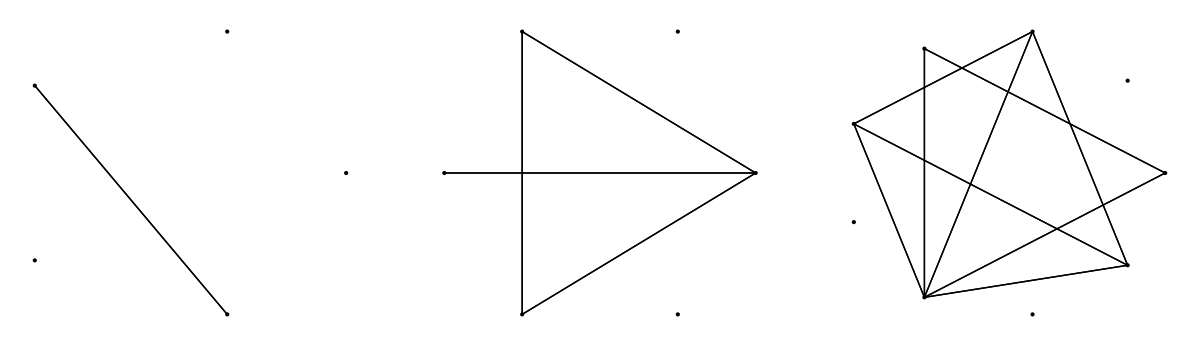

```mathematica
GraphicsRow[{
naloga4[5],naloga4[6],naloga4[9]
}]
```

## Rešitve

```mathematica
pomozna1a[{}]:=Point[{0,0}]

pomozna1a[{x_,sez___}]:=With[
{mali=pomozna1a[{sez}]},
Table[
Translate[Scale[mali,1/x],{Cos[2 π i/x],Sin[2 π i/x]}],
{i,x}
]
]

naloga1a[sez_]:=Graphics[pomozna1a[sez]]
```

```mathematica
naloga1b[1]:={{}}

naloga1b[n_]:=Join@@Table[Prepend[#,d]&/@naloga1b[n/d],{d,Rest[Divisors[n]]}]
```

```mathematica
naloga1c[n_]:=With[
{slike=naloga1a/@naloga1b[n]},
GraphicsGrid[ArrayReshape[slike,Table[Ceiling[Sqrt[Length[slike]]],{2}],Graphics[{}]]]
]
```

```mathematica
naloga2[sez_,k_]:=Table[sez[[Mod[1+k i,Length[sez],1]]],{i,0,Length[sez]-1}]
```

```mathematica
naloga3a[d_]:=SortBy[d,-Last[#]&]
```

```mathematica
pomozna3b[q_][{mn_,kum_},{x_,p_}]:=If[kum≥q,{mn,kum},{Append[mn,x],kum+p}]

naloga3b[d_,q_]:=With[
{urejene=naloga3a[d]},
Fold[pomozna3b[q],{{},0},urejene]
]
```

```mathematica
pomozna4[n_]:=Select[Tuples[{Range[n],Range[n]}],!CoprimeQ@@#&]
```

```mathematica
naloga4[n_]:=Graphics[{
Point[Table[{Cos[(2π i)/n],Sin[(2π i)/n]},{i,1,n}]],
Line[Table[{{Cos[(2π p[[1]])/n],Sin[(2π p[[1]])/n]},{Cos[(2π p[[2]])/n],Sin[(2π p[[2]])/n]}},{p,pomozna4[n]}]
]
}]
```